```mathematica
Table[k,{k,Keys[allGraphs2]}]
```

{0,1,2}

```mathematica
Table[allGraphs2[k,"graph"],{k,Keys[allGraphs2]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ff=Table[ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}]
```

{x^2,-x+x^2,x}

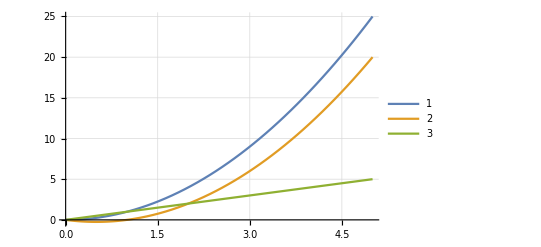

```mathematica
Plot[
ff,
{x,0,5},
GridLines->Automatic,
PlotLegends->Automatic
]
```

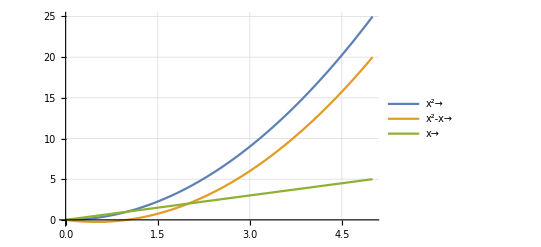

```mathematica
With[{formulae= Table[ChromaticPolynomial[allGraphs2[k,"graph"],x]->allGraphs2[k,"graph"],{k,Keys[allGraphs2]}]},
With[{short=Map[First,formulae]},

Plot[
short,
{x,0,5},
GridLines->Automatic,
PlotLegends->formulae
]
]
]
```

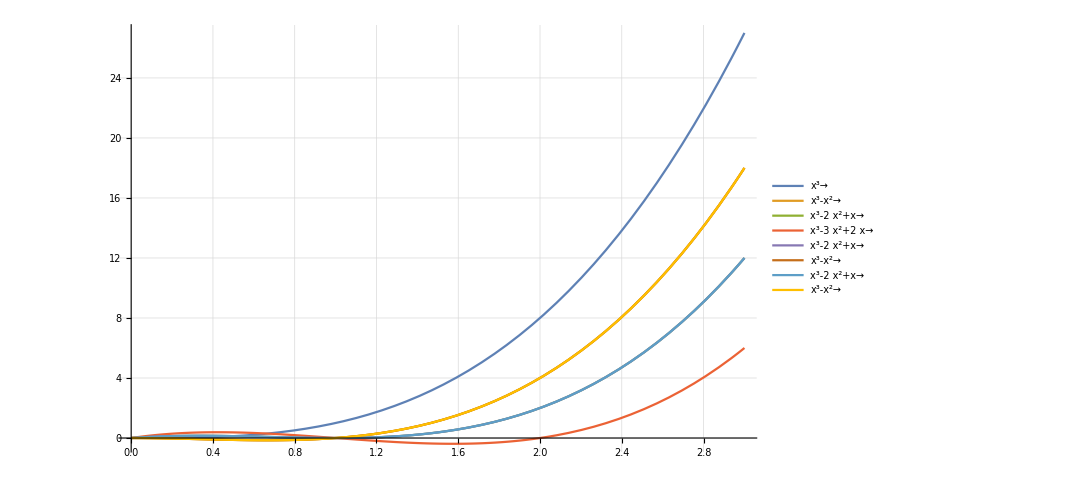

```mathematica
With[{formulae= Table[ChromaticPolynomial[allGraphs3[k,"graph"],x]->allGraphs3[k,"graph"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]},
With[{short=Map[First,formulae]},

Plot[
short,
{x,0,3},
GridLines->Automatic,
PlotLegends->formulae,
PlotRange->All,
ImageSize->800
]
]
]
```

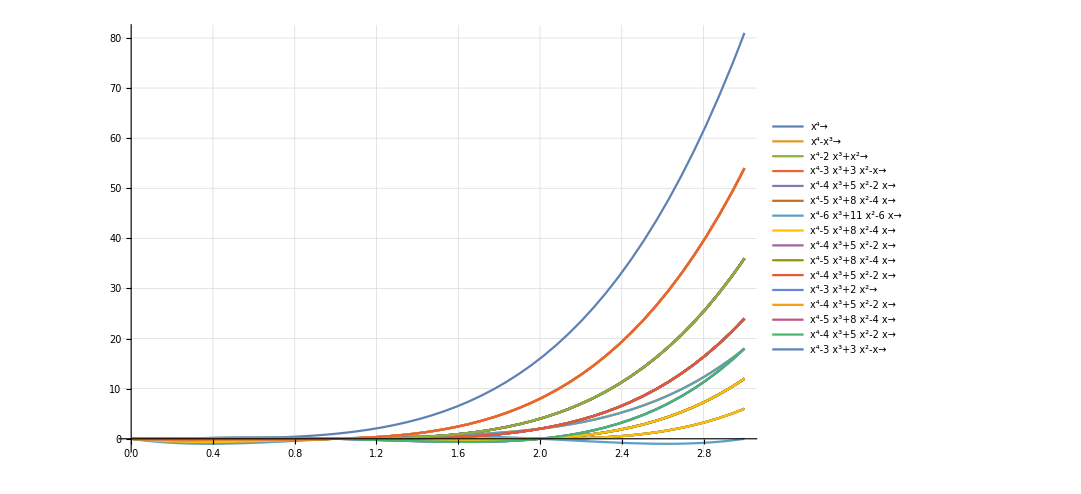

```mathematica
With[{formulae= Table[ChromaticPolynomial[allGraphs4[k,"graph"],x]->allGraphs4[k,"graph"],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]},
With[{short=Map[First,formulae]},

Plot[
short,
{x,0,3},
GridLines->Automatic,
PlotLegends->formulae,
PlotRange->All,
ImageSize->800
]
]
]
```

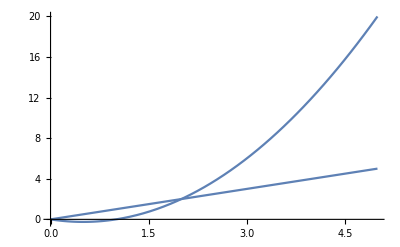

```mathematica
Show[
Map[
Plot[#,{x,0,5}]&,Table[ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,allGraphs2AtomKeys}]
]
]
```

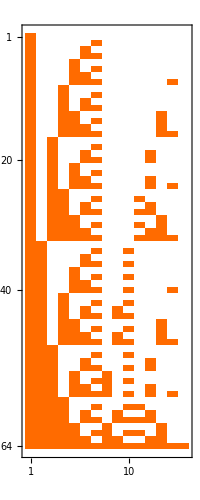

```mathematica
With[{keys=Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]},
Table[BaseCoeff4[k,"C"],{k,keys}]
]//Sort//MatrixPlot
```

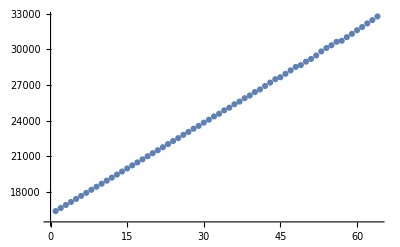

```mathematica
With[{keys=Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]},
Table[FromDigits[BaseCoeff4[k,"C"],2],{k,keys}]
]//Sort//ListPlot
```

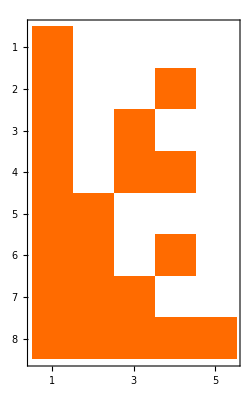

```mathematica
With[{keys=Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]},
Table[BaseCoeff3[k,"C"],{k,keys}]
]//Sort//MatrixPlot
```

```mathematica
With[{keys=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]},
Table[FromDigits[BaseCoeff[k,"C"],2],{k,keys}]
]//Sort//ListPlot
```

-Graphics-

```mathematica
With[{keys=Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]},
Table[FromDigits[BaseCoeff6[k,"C"],2],{k,keys}]
]//Sort//ListPlot
```

-Graphics-

```mathematica
With[{keys=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]},
Table[FromDigits[BaseCoeff[k,"C"],2],{k,keys}]
]//Sort//Differences//Tally//Sort
```

{{284063454550,1},{567942355354,1},{851468934622,1},{1132797682146,1},{1133409001984,1},{1408271185398,1},{1408815396352,1},{1676116007424,1},{1676119177728,1},{1683560135162,1},{1683632224768,1},{1683634584064,1},{1683635370496,1},{1942460454400,1},{1942464945664,1},{1942465738240,1},{1942466002432,1},{1958496763390,1},{1958499515904,1},{1958501744128,1},{1958503972352,1},{1958504103424,1},{1958504758784,1},{1958504889856,1},{1958505020928,1},{1958566622720,1},{1958571081216,1},{1958571865600,1},{1958572129792,1},{1959573249536,1},{1959575477760,1},{1959577705984,1},{1959578500608,1},{1959578631680,1},{1959578762752,1},{2164663582210,1},{2165274902048,1},{2173594041960,1},{2173597187712,1},{2173843472044,1},{2173847928560,1},{2173848714944,1},{2173848977152,1},{2173849108310,1},{2174393319264,1},{2182712459128,1},{2182715604864,1},{2182850084762,1},{2182924533664,1},{2182978666496,1},{2182983122944,1},{2182983909376,1},{2182984171520,1},{2189364953088,1},{2189366919168,1},{2189367312288,1},{2189367705536,1},{2189367967744,1},{2189368098816,1},{2189368360868,1},{2189370851268,1},{2191493103548,1},{2191497560064,1},{2191498346432,1},{2191498608640,1},{2191498739678,1},{2191506079712,1},{2191512109056,1},{2191515254784,1},{2197946499072,1},{2197948465152,3},{2197948727296,2},{2197948858336,1},{2197949251552,2},{2197949251584,1},{2197949513728,5},{2197949579234,1},{2197949644800,1},{2197949775872,2},{2197949906912,1},{2197950300128,2},{2197950562304,2},{2197952397312,1},{2198015574016,2},{2198015836160,2},{2198016360416,2},{2198016622592,4},{2198016884736,2},{2198017409000,2},{2198017671176,2},{2198290104296,1},{2198293250048,1},{2198424649704,1},{2198426615792,1},{2198427009024,1},{2198427402240,1},{2198427664384,1},{2198427795456,1},{2198428057580,1},{2198430547956,1},{2198539534316,1},{2198543990768,1},{2198544777216,1},{2198545039360,1},{2198545170422,1},{2198552444912,2},{2198552707056,2},{2198553231360,2},{2198553493504,4},{2198553755648,2},{2198554279928,2},{2198554542072,2},{2198560899072,1},{2198818586616,1},{2198821732352,1},{2198953132024,1},{2198955098112,1},{2198955491328,1},{2198955884544,1},{2198956146688,1},{2198956212218,1},{2198956277760,1},{2198956539896,1},{2198959030272,1},{2199009296380,1},{2199013752832,1},{2199014539264,1},{2199014801408,1},{2199014932478,1},{2199017684992,1},{2199019913216,1},{2199020240896,1},{2199022141440,1},{2199022206976,5},{2199022272512,1},{2199022469120,4},{2199022600192,1},{2199022927872,1},{2199022993408,5},{2199023058944,1},{2199023190016,1},{2199023255552,36},{2199023321088,9},{2199023386624,1},{2199023517696,4},{2199023648768,1},{2199023779840,9},{2199023845376,3},{2199024041984,4},{2199024304128,31},{2199024369664,9},{2199024828416,9},{2199024893954,3},{2199026139136,1},{2199028301824,1},{2199028629504,1},{2199030595584,1},{2199030661120,1},{2199030988800,1},{2199031382016,1},{2199031447552,1},{2199031644160,1},{2199031775232,1},{2199032037380,1},{2199034527748,1},{2199084793856,1},{2199089250304,1},{2199089315840,2},{2199089381376,1},{2199089577984,2},{2199090036736,1},{2199090102272,2},{2199090298880,1},{2199090364416,4},{2199090626560,2},{2199091150856,2},{2199091413000,2},{2199560126464,9},{2199560192000,3},{2199560650752,3},{2199560716288,1},{2199561175056,9},{2199561240592,3},{2199561699344,3},{2199561764882,1},{2199634632736,1},{2200091426816,1},{2200093655040,1},{2200095883264,1},{2200096669696,1},{2200096800768,1},{2200096931840,1},{2200096997376,27},{2200097062912,9},{2200097521696,9},{2200097587232,3},{2200098045952,27},{2200098111488,9},{2200098570272,9},{2200098635810,3},{2200633868288,9},{2200633934080,3},{2200634392608,3},{2200634458400,1},{2200634916880,9},{2200634982672,3},{2200635441200,3},{2200635506994,1},{2205940842600,1},{2205942808560,1},{2205943201824,1},{2205943594944,1},{2205943857152,1},{2205943988352,1},{2205944250380,1},{2205946740660,1},{2206068637680,2},{2206068899888,2},{2206069424160,2},{2206069686272,4},{2206069948480,2},{2206070472728,2},{2206070734840,2},{2206538399744,2},{2206538661952,2},{2206539186208,2},{2206539448320,4},{2206539710528,2},{2206540234784,2},{2206540496896,2},{2207953754216,1},{2207956924544,1},{2208203166892,1},{2208207658224,1},{2208208450752,1},{2208208715008,1},{2215059259512,1},{2215061225472,1},{2215061618784,1},{2215062011904,1},{2215062274048,1},{2215062405248,1},{2215062667352,1},{2215065157632,1},{2223724667904,1},{2223726649344,1},{2223727051680,1},{2223727443904,1},{2223727706112,1},{2223727838208,1},{2223728075684,1},{2223730581444,1},{2225852833212,1},{2225857289728,1},{2225858084288,1},{2225858346496,1},{2232306229248,1},{2232308195328,3},{2232308457472,2},{2232308596704,1},{2232308989920,2},{2232308989952,1},{2232309252096,5},{2232309383168,1},{2232309514240,2},{2232309637088,1},{2232310030304,2},{2232310292480,2},{2232312127488,1},{2232375304192,2},{2232375568384,2},{2232376100832,2},{2232376360960,4},{2232376625152,2},{2232377141224,2},{2232377401352,2},{2232649841128,1},{2232652986880,1},{2232784389096,1},{2232786354160,1},{2232786742272,1},{2232787138560,1},{2232787402752,1},{2232787534848,1},{2232787790828,1},{2232790284276,1},{2232899270124,1},{2232903728624,1},{2232904513024,1},{2232904777216,1},{2232912183280,2},{2232912447472,2},{2232912967680,2},{2232913231872,4},{2232913496064,2},{2232914016248,2},{2232914280440,2},{2233312870392,1},{2233314836480,1},{2233315227648,1},{2233315620864,1},{2233315885056,1},{2233316016128,1},{2233316276216,1},{2233318766592,1},{2233369034236,1},{2233373490688,1},{2233374277120,1},{2233374539264,1},{2233379979264,1},{2233381945344,5},{2233382207488,4},{2233382338560,1},{2233382731776,5},{2233382993920,36},{2233383059968,9},{2233383124992,1},{2233383256064,4},{2233383387136,1},{2233383518208,9},{2233383584256,3},{2233383780352,4},{2233384042496,31},{2233384108544,9},{2233384566784,9},{2233384632834,3},{2233385877504,1},{2233388368896,1},{2233390333952,1},{2233390728192,1},{2233391120384,1},{2233391382528,1},{2233391514624,1},{2233391776772,1},{2233394266116,1},{2233449054208,2},{2233449318400,2},{2233449842688,2},{2233450102784,4},{2233450366976,2},{2233450891272,2},{2233451151368,2},{2233919864832,9},{2233919930880,3},{2233920393216,3},{2233920459264,1},{2233920913424,9},{2233920979472,3},{2233921441808,3},{2233921507858,1},{2234456735744,27},{2234456801792,9},{2234457260064,9},{2234457326112,3},{2234457792512,27},{2234457858560,9},{2234458316832,9},{2234458382882,3},{2234993606656,9},{2234993672960,3},{2234994135072,3},{2234994201376,1},{2234994663440,9},{2234994729744,3},{2234995191856,3},{2234995258163,1},{2240300557416,1},{2240302538736,1},{2240302935072,1},{2240303331264,1},{2240303595520,1},{2240303727744,1},{2240303991820,1},{2240306501556,1},{2240428367856,2},{2240428632112,2},{2240429160480,2},{2240429424640,4},{2240429688896,2},{2240430217240,2},{2240430481400,2},{2240898129920,2},{2240898392128,2},{2240898924576,2},{2240899186688,4},{2240899448896,2},{2240899981344,2},{2240900243456,2},{2249418989688,1},{2249420955648,1},{2249421355104,1},{2249421748224,1},{2249422012416,1},{2249422143616,1},{2249422428248,1},{2249424918528,1},{2483630962016,1},{2491950095736,1},{2491953249664,1},{2508056231416,1},{2508059377152,1},{2767040084384,1},{3050499538400,1}}